```mathematica
sumIntDigits[n_, b_]:=Total[IntegerDigits[n, b]]
twistExpSumList[n_, b_, p_, q_] := Prepend[Accumulate[(Exp[2.0*Pi*I*(sumIntDigits[#, b]/p + (#/q))]&/@Range[n])], 0]
twistVisualizer[n_, b_, p_, q_]:=ListLinePlot[ReIm /@ twistExpSumList[n,b, p, q], PlotStyle->Thick]
expSumList[n_ ,b_, p_]:=Prepend[Accumulate[Exp[2.0*Pi*I*sumIntDigits[#, b]/p]&/@Range[n]], 0]
visualizer[n_, b_, p_]:=ListLinePlot[ReIm /@ expSumList[n,b, p], PlotStyle->Thick]
chunkVisualizer[n1_, n2_, b_, p_, c_]:=ListLinePlot[ReIm /@ Take[expSumList[n2,b, p], {n1, n2+1}], PlotStyle->{Thick, c}]
pointVisualizer[n_, b_, p_]:=ListPlot[ReIm /@ expSumList[n,b, p], PlotStyle->{PointSize[Large], Red}]
```

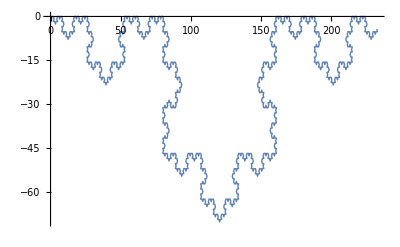

```mathematica
twistVisualizer[1000, 2, 2, 3]
```

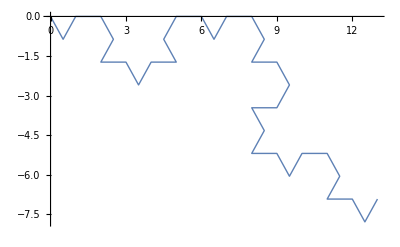
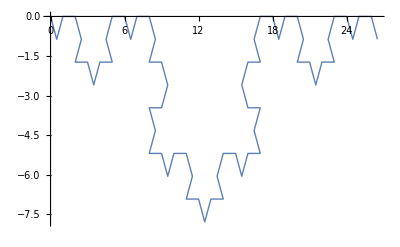
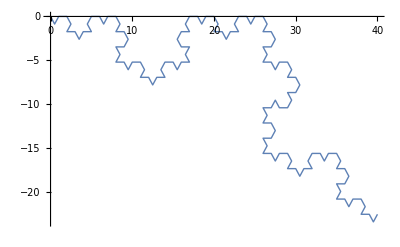
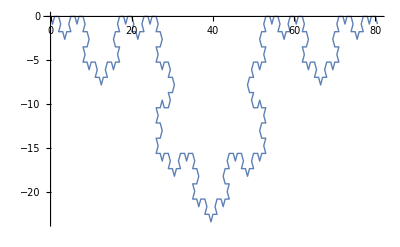
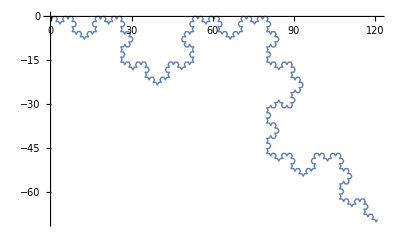
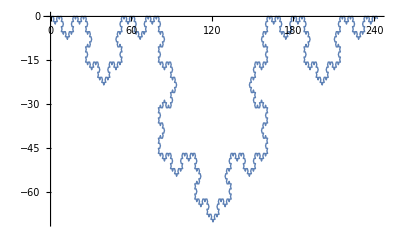
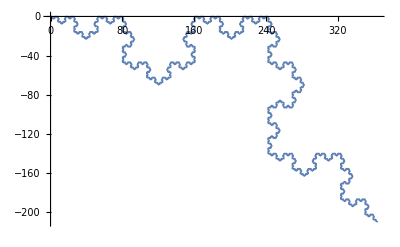
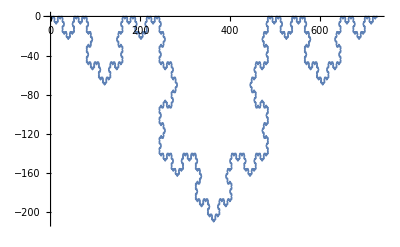

```mathematica
Table[twistVisualizer[2^k, 2, 2, 3], {k, 5, 15}]
```

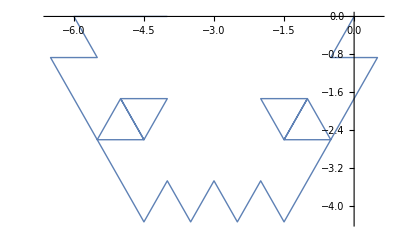
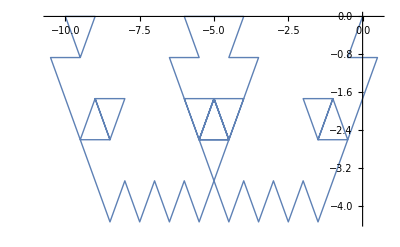
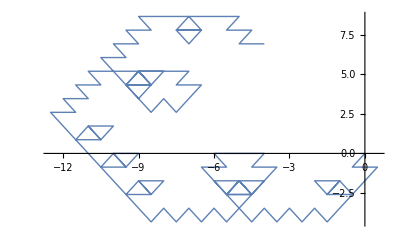
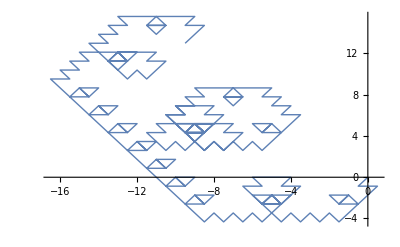
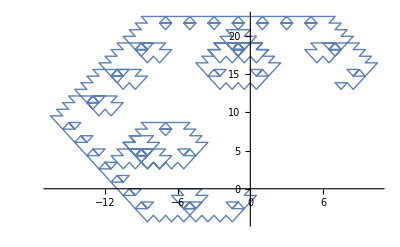
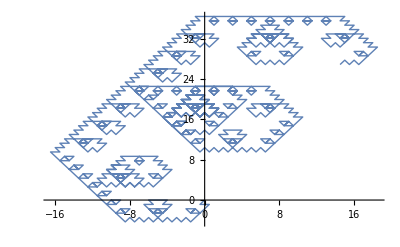
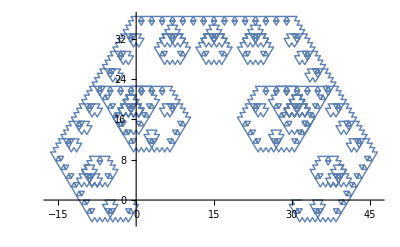
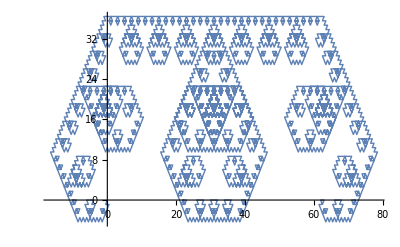

```mathematica
Table[twistVisualizer[2^k, 2, 3, 3], {k, 5, 15}]
```

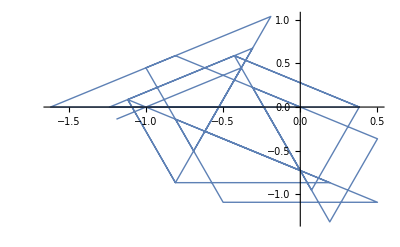
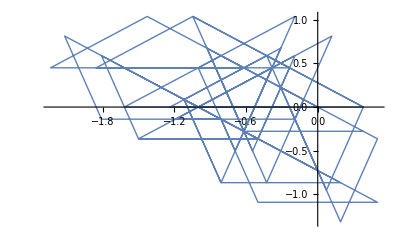
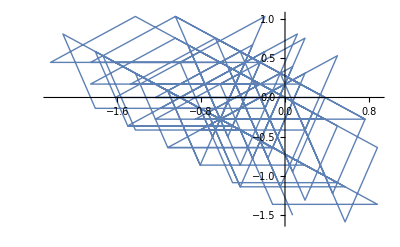
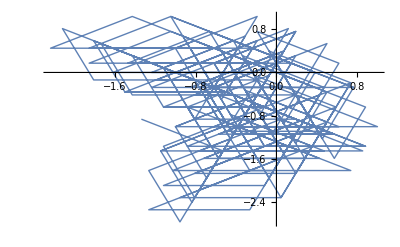
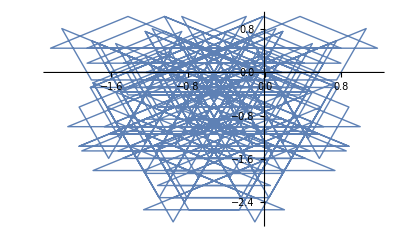
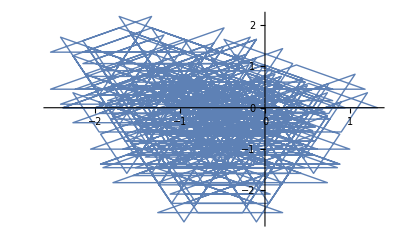
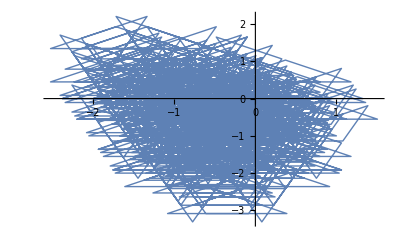
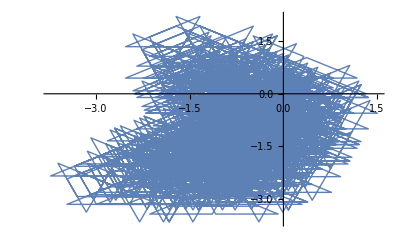

```mathematica
Table[twistVisualizer[2^k, 2, 5, 5], {k, 5, 15}]
```

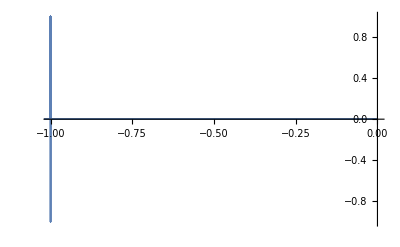
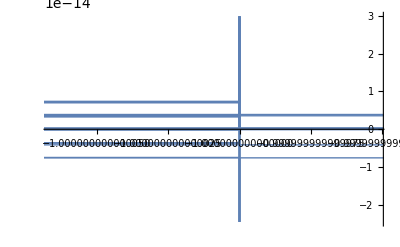
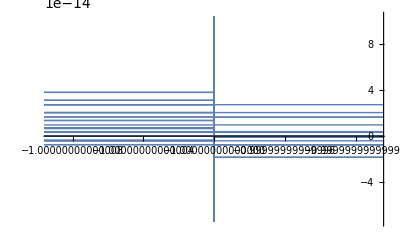
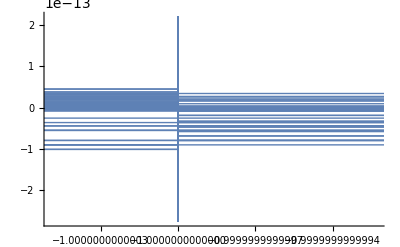
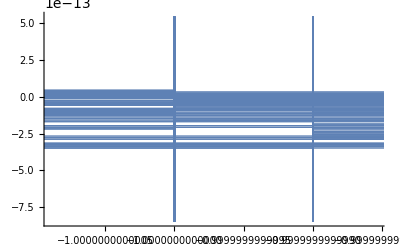
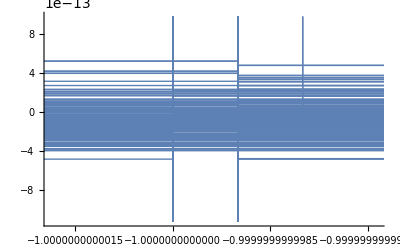
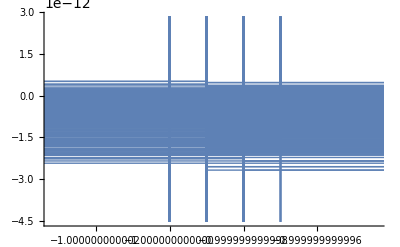
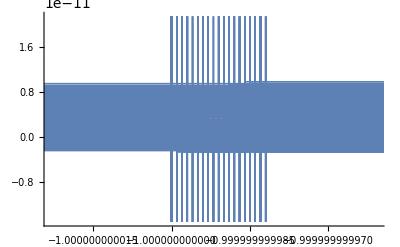
{{{{32,3},-Graphics-},{{64,3},-Graphics-},{{128,3},-Graphics-},{{256,3},-Graphics-},{{512,3},-Graphics-},{{1024,3},-Graphics-},{{2048,3},-Graphics-},{{4096,3},-Graphics-}},{{{32,4},-Graphics-},{{64,4},-Graphics-},{{128,4},-Graphics-},{{256,4},-Graphics-},{{512,4},-Graphics-},{{1024,4},-Graphics-},{{2048,4},-Graphics-},{{4096,4},-Graphics-}},{{{32,5},-Graphics-},{{64,5},-Graphics-},{{128,5},-Graphics-},{{256,5},-Graphics-},{{512,5},-Graphics-},{{1024,5},-Graphics-},{{2048,5},-Graphics-},{{4096,5},-Graphics-}},{{{32,6},-Graphics-},{{64,6},-Graphics-},{{128,6},-Graphics-},{{256,6},-Graphics-},{{512,6},-Graphics-},{{1024,6},-Graphics-},{{2048,6},-Graphics-},{{4096,6},-Graphics-}},{{{32,7},-Graphics-},{{64,7},-Graphics-},{{128,7},-Graphics-},{{256,7},-Graphics-},{{512,7},-Graphics-},{{1024,7},-Graphics-},{{2048,7},-Graphics-},{{4096,7},-Graphics-}},{{{32,8},-Graphics-},{{64,8},-Graphics-},{{128,8},-Graphics-},{{256,8},-Graphics-},{{512,8},-Graphics-},{{1024,8},-Graphics-},{{2048,8},-Graphics-},{{4096,8},-Graphics-}},{{{32,9},-Graphics-},{{64,9},-Graphics-},{{128,9},-Graphics-},{{256,9},-Graphics-},{{512,9},-Graphics-},{{1024,9},-Graphics-},{{2048,9},-Graphics-},{{4096,9},-Graphics-}},{{{32,10},-Graphics-},{{64,10},-Graphics-},{{128,10},-Graphics-},{{256,10},-Graphics-},{{512,10},-Graphics-},{{1024,10},-Graphics-},{{2048,10},-Graphics-},{{4096,10},-Graphics-}},{{{32,11},-Graphics-},{{64,11},-Graphics-},{{128,11},-Graphics-},{{256,11},-Graphics-},{{512,11},-Graphics-},{{1024,11},-Graphics-},{{2048,11},-Graphics-},{{4096,11},-Graphics-}},{{{32,12},-Graphics-},{{64,12},-Graphics-},{{128,12},-Graphics-},{{256,12},-Graphics-},{{512,12},-Graphics-},{{1024,12},-Graphics-},{{2048,12},-Graphics-},{{4096,12},-Graphics-}},{{{32,13},-Graphics-},{{64,13},-Graphics-},{{128,13},-Graphics-},{{256,13},-Graphics-},{{512,13},-Graphics-},{{1024,13},-Graphics-},{{2048,13},-Graphics-},{{4096,13},-Graphics-}},{{{32,14},-Graphics-},{{64,14},-Graphics-},{{128,14},-Graphics-},{{256,14},-Graphics-},{{512,14},-Graphics-},{{1024,14},-Graphics-},{{2048,14},-Graphics-},{{4096,14},-Graphics-}},{{{32,15},-Graphics-},{{64,15},-Graphics-},{{128,15},-Graphics-},{{256,15},-Graphics-},{{512,15},-Graphics-},{{1024,15},-Graphics-},{{2048,15},-Graphics-},{{4096,15},-Graphics-}}}

```mathematica
Table[{{2^k, q},twistVisualizer[2^k, 2, q, q]}, {q, 3, 15}, {k, 5, 12}]
```

```mathematica
Table[twistVisualizer[5000, 2, q-1, q], {q, 3, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[twistVisualizer[5000, 2, q-1, q], {q, 3, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
qList = RandomReal[{2, 5}, 10]
```

{3.17184,4.01164,4.0017,2.36373,4.48096,3.7625,3.19513,4.95292,2.37451,3.31002}

```mathematica
Table[{2^k, q, twistVisualizer[2^k, 2, q, q]},{q, qList},{k, 5, 12}]
```

{{{32,3.17184,-Graphics-},{64,3.17184,-Graphics-},{128,3.17184,-Graphics-},{256,3.17184,-Graphics-},{512,3.17184,-Graphics-},{1024,3.17184,-Graphics-},{2048,3.17184,-Graphics-},{4096,3.17184,-Graphics-}},{{32,4.01164,-Graphics-},{64,4.01164,-Graphics-},{128,4.01164,-Graphics-},{256,4.01164,-Graphics-},{512,4.01164,-Graphics-},{1024,4.01164,-Graphics-},{2048,4.01164,-Graphics-},{4096,4.01164,-Graphics-}},{{32,4.0017,-Graphics-},{64,4.0017,-Graphics-},{128,4.0017,-Graphics-},{256,4.0017,-Graphics-},{512,4.0017,-Graphics-},{1024,4.0017,-Graphics-},{2048,4.0017,-Graphics-},{4096,4.0017,-Graphics-}},{{32,2.36373,-Graphics-},{64,2.36373,-Graphics-},{128,2.36373,-Graphics-},{256,2.36373,-Graphics-},{512,2.36373,-Graphics-},{1024,2.36373,-Graphics-},{2048,2.36373,-Graphics-},{4096,2.36373,-Graphics-}},{{32,4.48096,-Graphics-},{64,4.48096,-Graphics-},{128,4.48096,-Graphics-},{256,4.48096,-Graphics-},{512,4.48096,-Graphics-},{1024,4.48096,-Graphics-},{2048,4.48096,-Graphics-},{4096,4.48096,-Graphics-}},{{32,3.7625,-Graphics-},{64,3.7625,-Graphics-},{128,3.7625,-Graphics-},{256,3.7625,-Graphics-},{512,3.7625,-Graphics-},{1024,3.7625,-Graphics-},{2048,3.7625,-Graphics-},{4096,3.7625,-Graphics-}},{{32,3.19513,-Graphics-},{64,3.19513,-Graphics-},{128,3.19513,-Graphics-},{256,3.19513,-Graphics-},{512,3.19513,-Graphics-},{1024,3.19513,-Graphics-},{2048,3.19513,-Graphics-},{4096,3.19513,-Graphics-}},{{32,4.95292,-Graphics-},{64,4.95292,-Graphics-},{128,4.95292,-Graphics-},{256,4.95292,-Graphics-},{512,4.95292,-Graphics-},{1024,4.95292,-Graphics-},{2048,4.95292,-Graphics-},{4096,4.95292,-Graphics-}},{{32,2.37451,-Graphics-},{64,2.37451,-Graphics-},{128,2.37451,-Graphics-},{256,2.37451,-Graphics-},{512,2.37451,-Graphics-},{1024,2.37451,-Graphics-},{2048,2.37451,-Graphics-},{4096,2.37451,-Graphics-}},{{32,3.31002,-Graphics-},{64,3.31002,-Graphics-},{128,3.31002,-Graphics-},{256,3.31002,-Graphics-},{512,3.31002,-Graphics-},{1024,3.31002,-Graphics-},{2048,3.31002,-Graphics-},{4096,3.31002,-Graphics-}}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 2.97422, 2.97422]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 3, 3]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 113/38, 113/38]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Manipulate[list = ReIm /@ twistExpSumList[2^k, 2, 2.97422, 2.97422];
maxRange  = 1.1*Max[Abs[list]];
ListLinePlot[Take[list, Floor[2^k]],PlotRange->{{-maxRange, maxRange}, {-maxRange, maxRange}}, AspectRatio->1],{k, 5, 15,Animator, AnimationRate->1, AnimationRunning->True}]
```

```mathematica
Table[{twistVisualizer[5000, 2, q, q]}, {q, 3, 15}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
Table[{twistVisualizer[5000, 2, 2, q]}, {q, 3, 15}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
irrationalList = {Sqrt[2], Sqrt[3], Sqrt[6], Pi, EulerGamma, Log[2.], E}
```

{√2,√3,√6,π,EulerGamma,0.693147,ⅇ}

```mathematica
Table[twistVisualizer[5000, 3, 2, q], {q, irrationalList}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
N[E]
```

2.71828

```mathematica
Table[{b, twistVisualizer[5000, b, 2, q]}, {b, 2, 10}, {q, irrationalList}]
```

{{{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-}},{{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-}},{{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-}},{{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-}},{{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-}},{{7,-Graphics-},{7,-Graphics-},{7,-Graphics-},{7,-Graphics-},{7,-Graphics-},{7,-Graphics-},{7,-Graphics-}},{{8,-Graphics-},{8,-Graphics-},{8,-Graphics-},{8,-Graphics-},{8,-Graphics-},{8,-Graphics-},{8,-Graphics-}},{{9,-Graphics-},{9,-Graphics-},{9,-Graphics-},{9,-Graphics-},{9,-Graphics-},{9,-Graphics-},{9,-Graphics-}},{{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-}}}

```mathematica
Manipulate[twistVisualizer[5000, b, 2, q], {b, 2, 10, 1,SetterBar}, {q, irrationalList, SetterBar}]
```

```mathematica
N[EulerGamma]
```

0.577216

```mathematica
(* Overall, trying to see if pattern of odd bases is a single circle for any q *)
Table[twistVisualizer[3000, 5, 2, q], {q, 2, 15,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Here we can see that if we generate random real numbers, the pattern is holding to an extent *)
Table[{q, twistVisualizer[3000, 5, 2, q]}, {q, RandomReal[{1, 10}, 10]}]
```

{{1.35015,-Graphics-},{6.92068,-Graphics-},{1.90082,-Graphics-},{4.89043,-Graphics-},{8.82207,-Graphics-},{5.54754,-Graphics-},{8.03082,-Graphics-},{7.39535,-Graphics-},{2.4682,-Graphics-},{9.71648,-Graphics-}}

We can see here so far that actual integers are not creating the circles we need for some reason, and that rather, it is some random real numbers that are indeed doing the trick. So far, I will hypothesize that the number needs to be a decimal for this pattern to hold. Now, onto negative numbers.

```mathematica
Table[{q, twistVisualizer[3000, 5, 2, q]}, {q, RandomReal[{-10, -1}, 10]}]
```

{{-8.39838,-Graphics-},{-1.53876,-Graphics-},{-4.19252,-Graphics-},{-8.5636,-Graphics-},{-7.77012,-Graphics-},{-7.42209,-Graphics-},{-8.57688,-Graphics-},{-4.51077,-Graphics-},{-3.4181,-Graphics-},{-1.74103,-Graphics-}}

This pattern also appears to work with negative numbers (I actually ran a lot more tests with this than I’ve shown). So, now we need to actually prove that there is some special properties with these decimals that are creating this circular visualizations, as opposed to the other convex shapes we get when we run this code for integers.

```mathematica
(* Testing the digits of the decimal values *)
randomlist = RandomReal[{-10, 10}, 10]
```

{-0.500872,5.83825,-0.551849,-4.59347,-2.64689,-9.84136,-3.1626,-5.27018,7.76883,7.1371}

```mathematica
sumlist = Total[#]& /@ (First /@ RealDigits[randomlist])
```

{53,71,82,77,88,50,77,76,93,82}

```mathematica
Table[{q, twistVisualizer[3000, 5, 2, q]}, {q, randomlist}]
```

{{-0.500872,-Graphics-},{5.83825,-Graphics-},{-0.551849,-Graphics-},{-4.59347,-Graphics-},{-2.64689,-Graphics-},{-9.84136,-Graphics-},{-3.1626,-Graphics-},{-5.27018,-Graphics-},{7.76883,-Graphics-},{7.1371,-Graphics-}}

Currently, I really can not find a pattern as to why this is the way it is, but I will continue to experiment in the future, because this is an interesting pattern.